```mathematica
npsmat[g_]:=Block[{vs=VertexList[g]},
Table[Length[FindPath[g,v,w,∞,All]],{v,vs},{w,vs}]]
```

```mathematica
nthor[g_,n_]:=Block[{es=EdgeList[g],len=EdgeCount[g]},
Block[{digs=PadLeft[IntegerDigits[n,2],len]},
Graph[Table[Piecewise[{{es[[i]][[1]]->es[[i]][[2]], digs[[i]]==0}, {es[[i]][[2]]->es[[i]][[1]], True}}],{i,1,len}]]]]
```

```mathematica
Table[VertexConnectivity[nthor[CompleteGraph[4],j]],{j,0,2^6-1}]
```

{0,0,0,0,0,0,0,0,1,0,1,0,1,1,0,0,0,1,1,1,0,1,0,0,1,1,1,0,0,1,0,0,0,0,1,0,0,1,1,1,0,0,1,0,1,1,1,0,0,0,1,1,0,1,0,1,0,0,0,0,0,0,0,0}

```mathematica
[0,n]->{n-j,n-i}
```

```mathematica
[1,L]->{n+1-j,n+1-i}
```

```mathematica
cxsym[mat_]:=Block[{l=Length[mat]},
And@@Map[And@@#&,Table[mat[[i,j]]==mat[[l+1-j,l+1-i]],{i,1,l},{j,1,l}]]]
```

```mathematica
cxsym[({{0, 1, 1}, {0, 0, 1}, {1, 0, 0}})]
```

True

```mathematica
gcx[g_]:=cxsym[AdjacencyMatrix[g]]
```

```mathematica
Map[First,Select[Table[{j,(VertexConnectivity[nthor[CompleteGraph[4],j]]>0)&&(gcx[nthor[CompleteGraph[4],j]])},{j,0,2^6-1}],Last]]
```

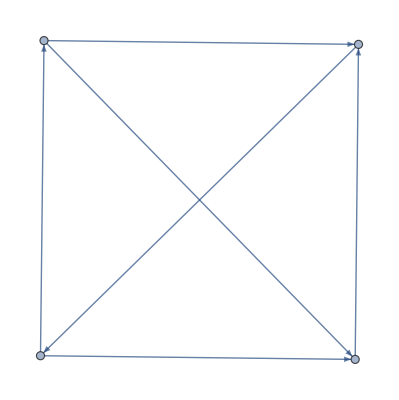

```mathematica
AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]
```

```mathematica
Evaluate[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]
```

{{0,1,1,0},{0,0,1,1},{0,0,0,1},{1,0,0,0}}

{(0 | 1 | 2 | 3
2 | 0 | 2 | 2
1 | 1 | 0 | 1
1 | 1 | 2 | 0),(0 | 1 | 2 | 3
0 | 0 | 1 | 2
0 | 0 | 0 | 1
0 | 0 | 0 | 0),(0 | 1 | 1 | 2
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0),(0 | 0 | 1 | 0
1 | 0 | 2 | 1
0 | 0 | 0 | 0
1 | 0 | 1 | 0),(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 1 | 0 | 1
1 | 1 | 1 | 0)}

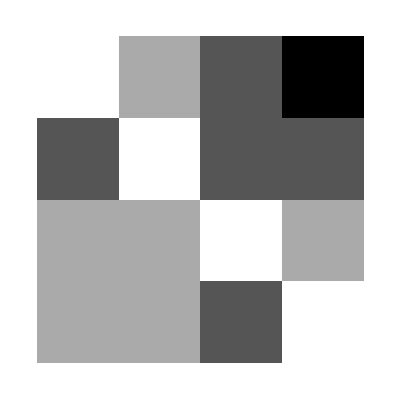
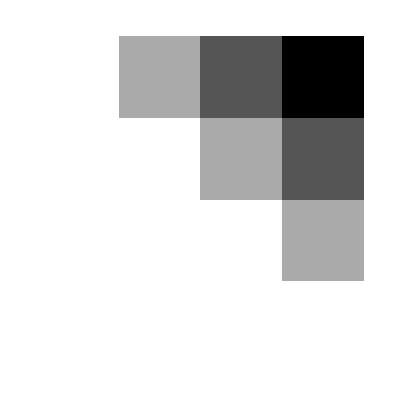
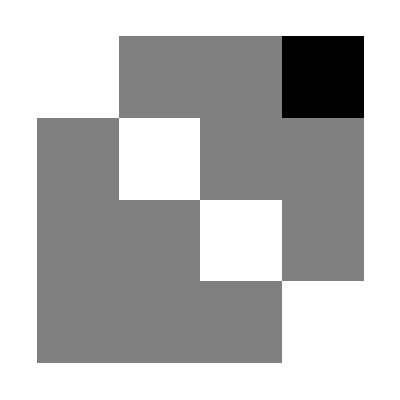
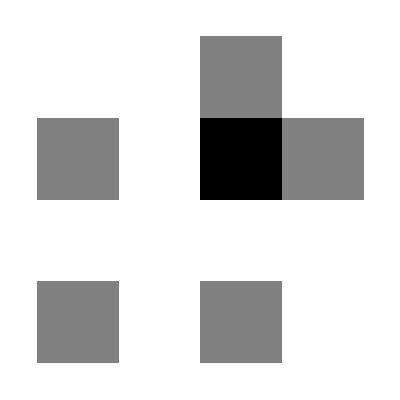
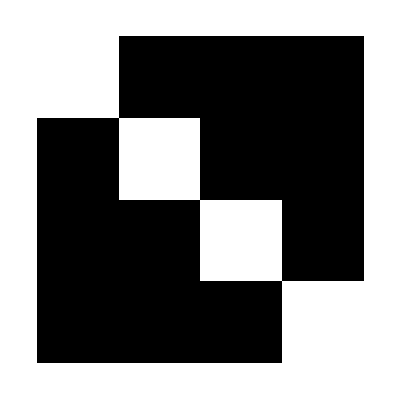

```mathematica
{MatrixForm[npsmat[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]]],
MatrixForm[npsmat[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {0*1, 0, 0, 0}})]]],
MatrixForm[npsmat[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 0*1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]]],
MatrixForm[npsmat[AdjacencyGraph[({{0, 0*1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 0*1}, {1, 0, 0, 0}})]]],
MatrixForm[npsmat[AdjacencyGraph[({{0, 1, 0*1, 0}, {0, 0, 1, 0*1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]]]}
Map[ArrayPlot[First[#]]&,%]
```

```mathematica
First[MatrixForm[{{1,2},{3,4}}]]
```

{{1,2},{3,4}}

```mathematica
{MatrixForm[npsmat[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]]],MatrixForm[npsmat[AdjacencyGraph[({{0, 0*1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 0*1}, {1, 0, 0, 0}})]]]}
```

{(0 | 1 | 2 | 3
2 | 0 | 2 | 2
1 | 1 | 0 | 1
1 | 1 | 2 | 0),(0 | 0 | 1 | 0
1 | 0 | 2 | 1
0 | 0 | 0 | 0
1 | 0 | 1 | 0)}

(1 | 1 | 0 | 0
0 | 1 | 0 | 0
1 | 1 | 1 | 1
1 | 1 | 0 | 1)

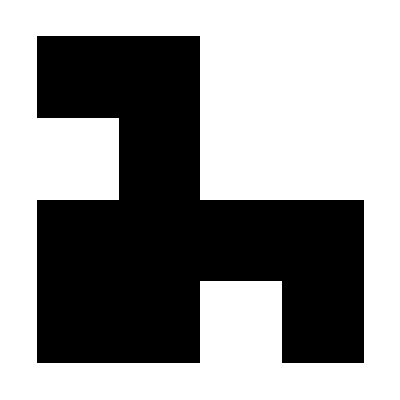

```mathematica
Map[Piecewise[{{1, #==0}, {0, True}}]&,MatrixForm[npsmat[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]]-npsmat[AdjacencyGraph[({{0, 1, 0*1, 0}, {0, 0, 0*1, 0*1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]]],{3}]
ArrayPlot[%]
```

```mathematica
ArrayPlot[MatrixForm[npsmat[nthor[CompleteGraph[4],#]]]]
```

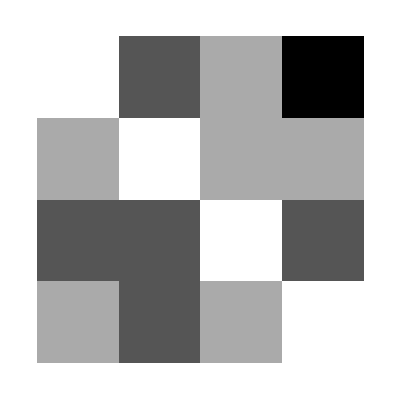
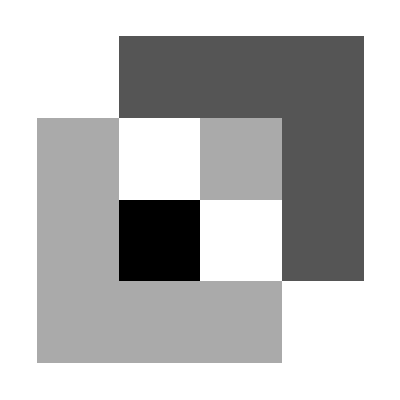
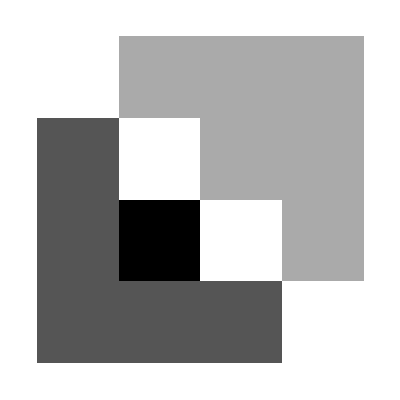
{(0 | 1 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1
1 | 0 | 0 | 0),-Graphics-,(0 | 1 | 2 | 3
2 | 0 | 2 | 2
1 | 1 | 0 | 1
1 | 1 | 2 | 0),-Graphics-}
{(0 | 1 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 1
1 | 0 | 0 | 0),-Graphics-,(0 | 2 | 1 | 3
1 | 0 | 1 | 1
2 | 2 | 0 | 2
1 | 2 | 1 | 0),-Graphics-}
{(0 | 1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 1
0 | 1 | 0 | 0),-Graphics-,(0 | 2 | 2 | 2
1 | 0 | 1 | 2
1 | 3 | 0 | 2
1 | 1 | 1 | 0),-Graphics-}
{(0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 1
1 | 1 | 0 | 0),-Graphics-,(0 | 1 | 1 | 1
2 | 0 | 1 | 1
2 | 3 | 0 | 1
2 | 2 | 2 | 0),-Graphics-}
{(0 | 1 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1
1 | 0 | 0 | 0),-Graphics-,(0 | 1 | 2 | 3
2 | 0 | 2 | 2
1 | 1 | 0 | 1
1 | 1 | 2 | 0),-Graphics-}
{(0 | 1 | 0 | 1
0 | 0 | 1 | 0
1 | 0 | 0 | 1
0 | 1 | 0 | 0),-Graphics-,(0 | 2 | 2 | 2
1 | 0 | 1 | 2
1 | 3 | 0 | 2
1 | 1 | 1 | 0),-Graphics-}
{(0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 1
1 | 1 | 0 | 0),-Graphics-,(0 | 1 | 1 | 1
2 | 0 | 1 | 1
2 | 3 | 0 | 1
2 | 2 | 2 | 0),-Graphics-}
{(0 | 1 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 1
1 | 0 | 0 | 0),-Graphics-,(0 | 2 | 1 | 3
1 | 0 | 1 | 1
2 | 2 | 0 | 2
1 | 2 | 1 | 0),-Graphics-}

```mathematica
Map[{MatrixForm[AdjacencyMatrix[nthor[CompleteGraph[4],#]]],ArrayPlot[AdjacencyMatrix[nthor[CompleteGraph[4],#]]],MatrixForm[npsmat[nthor[CompleteGraph[4],#]]],ArrayPlot[npsmat[nthor[CompleteGraph[4],#]]]}&,{8,12,18,26,34,44,46,50}]//Column
```

```mathematica
{VertexList[nthor[CompleteGraph[4],8]],EdgeList[nthor[CompleteGraph[4],8]]}
```

{{1,2,3,4},{1->2,1->3,4->1,2->3,2->4,3->4}}

```mathematica
{MatrixForm[AdjacencyMatrix[nthor[CompleteGraph[4],8]]],MatrixForm[npsmat[nthor[CompleteGraph[4],8]]]}
```

{(0 | 1 | 1 | 0
0 | 0 | 1 | 1
0 | 0 | 0 | 1
1 | 0 | 0 | 0),(0 | 1 | 2 | 3
2 | 0 | 2 | 2
1 | 1 | 0 | 1
1 | 1 | 2 | 0)}

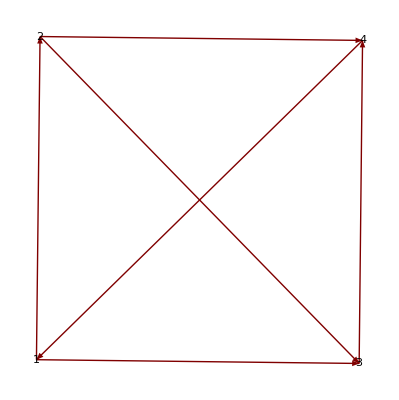

```mathematica
GraphPlot[nthor[CompleteGraph[4],8],VertexLabeling->True]
```

```mathematica
dropN[m_]:=Drop[m,{+1},{}]
dropS[m_]:=Drop[m,{-1},{}]
dropE[m_]:=Drop[m,{},-1]
dropW[m_]:=Drop[m,{},+1]
submats[m_]:=If[Length[m]≤1,m,
Join[{m},submats[dropN[dropW[m]]],
submats[dropN[dropE[m]]],
submats[dropS[dropW[m]]],
submats[dropS[dropE[m]]]]]
Map[MatrixForm,submats[({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})]]
```

{(1 | 2 | 3
4 | 5 | 6
7 | 8 | 9),(5 | 6
8 | 9),(9),(8),(6),(5),(4 | 5
7 | 8),(8),(7),(5),(4),(2 | 3
5 | 6),(6),(5),(3),(2),(1 | 2
4 | 5),(5),(4),(2),(1)}

```mathematica
enummat[m_]:=Table[{i,j,m[[i,j]]},{i,1,Length[m]},{j,1,Length[m]}]
enummat[({{1, 2}, {3, 4}})]//MatrixForm
```

((1
1
1) | (1
2
2)
(2
1
3) | (2
2
4))

```mathematica
cx[m_]:=Map[Reverse,Transpose[Map[Reverse,m]]]
```

```mathematica
cxQ[m_]:=m==cx[m]
```

```mathematica
extractCx[m_]:=If[cxQ[Map[#[[3]]&,m,{2}]],Block[{l=Length[m]},Table[{Take[m[[i,j]],2],Take[m[[l+1-j,l+1-i]],2]},{i,1,l},{j,1,l}]],{}]
```

```mathematica
allSyms[m_]:=Select[DeleteDuplicates[Map[Sort,Flatten[Map[extractCx,Select[submats[enummat[m]],ListQ[First[First[#]]]&]],2]]],(#[[1]]≠#[[2]])&&(#[[1,1]]≠#[[1,2]])&]
showAllSyms[m_]:=enum2mat[allSyms[m]]
```

```mathematica
showAllSyms[({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}})]//MatrixForm
```

(0 | 1 | 0
2 | 0 | 1
0 | 2 | 0)

```mathematica
enum2mat[{{{1,1},{3,3}},{{1,2},{2,3}},{{2,1},{3,2}},{{2,2},{3,3}},{{1,1},{2,2}}}]//MatrixForm
```

(1 | 2 | 0
3 | 4 | 2
0 | 3 | 1)

```mathematica
enum2mat[ps_]:=Block[{mx=Max[Flatten[ps]]},SparseArray[Flatten[Table[{ps[[k,1]]->k,ps[[k,2]]->k},{k,1,Length[ps]}],1],{mx,mx}]]
```



```mathematica
AdjacencyGraph[({{0, 1, 0}, {1, 0, 1}, {0, 1, 0}})]
```

```mathematica
showAllSyms[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]//MatrixForm
```

(0 | 1 | 2 | 0
3 | 0 | 5 | 2
4 | 6 | 0 | 1
0 | 4 | 3 | 0)

```mathematica
allSyms[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]
```

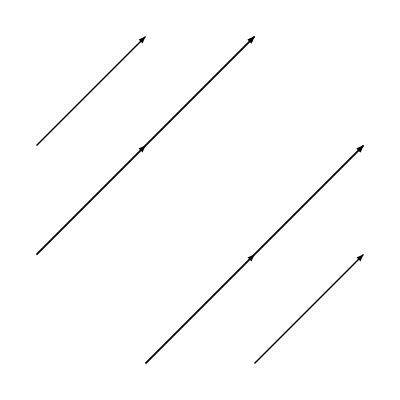

```mathematica
Graphics[Map[Arrow,{{{1,2},{3,4}},{{1,3},{2,4}},{{2,1},{4,3}},{{3,1},{4,2}},{{2,3},{3,4}},{{3,2},{4,3}},{{2,1},{3,2}},{{1,2},{2,3}}}]]
```

```mathematica
Transpose[Map[Reverse,({{1, 2, 3}, {4, 5, 6}, {7, 8, 9}})]]//MatrixForm
```

(3 | 6 | 9
2 | 5 | 8
1 | 4 | 7)

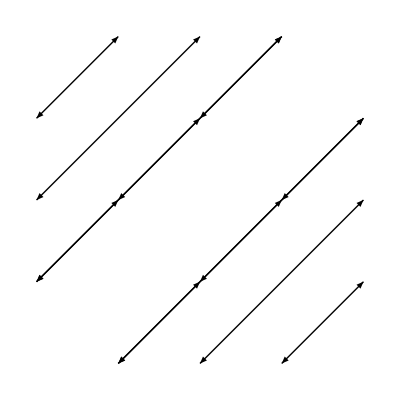
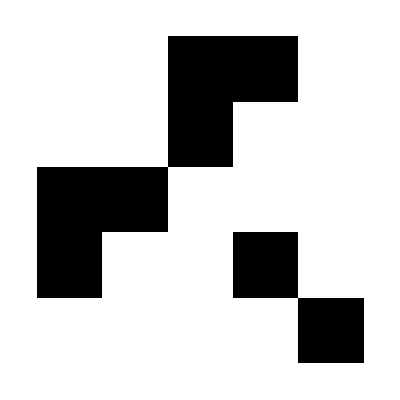
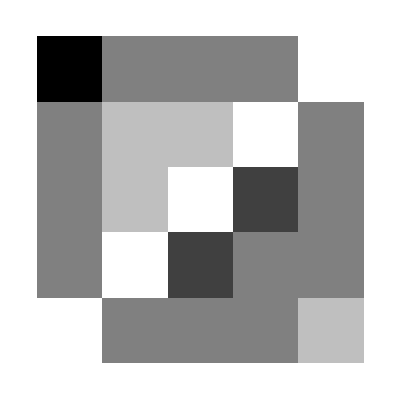
{-Graphics-,-Graphics-,-Graphics-,(4 | 2 | 2 | 2 | 0
2 | 1 | 1 | 0 | 2
2 | 1 | 0 | 3 | 2
2 | 0 | 3 | 2 | 2
0 | 2 | 2 | 2 | 1),(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
1 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)}

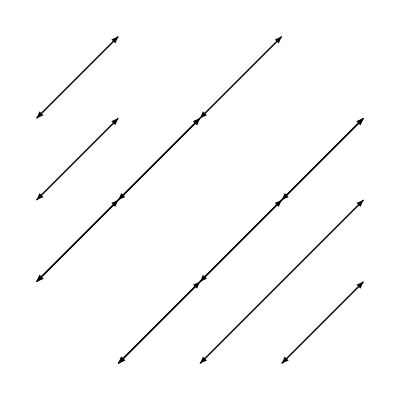
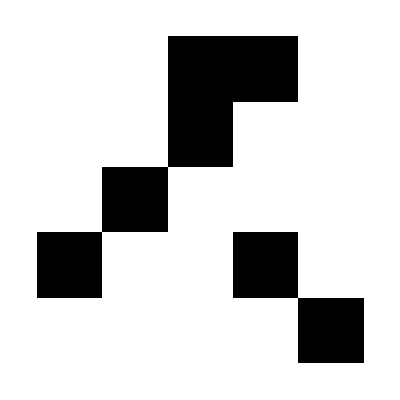
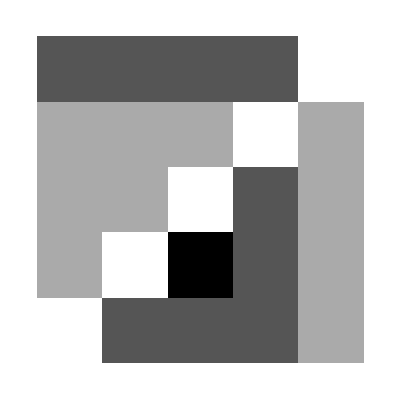
{-Graphics-,-Graphics-,-Graphics-,(2 | 2 | 2 | 2 | 0
1 | 1 | 1 | 0 | 1
1 | 1 | 0 | 2 | 1
1 | 0 | 3 | 2 | 1
0 | 2 | 2 | 2 | 1),(0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1)}

```mathematica
sumup[m_]:={Graphics[Join[{Arrowheads[{-.1,.1}]},Map[Arrow,allSyms[m]]]],ArrayPlot[Transpose[Map[Reverse,m]]],ArrayPlot[Transpose[Map[Reverse,npsmat[AdjacencyGraph[m]]]]],MatrixForm[Transpose[Map[Reverse,npsmat[AdjacencyGraph[m]]]]],MatrixForm[Transpose[Map[Reverse,m]]]}
sumup[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})]
sumup[({{0, 1, 0, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})]
```

```mathematica
npsmat[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})]]//MatrixForm
```

(0 | 2 | 2 | 2 | 4
2 | 0 | 1 | 1 | 2
2 | 3 | 0 | 1 | 2
2 | 2 | 3 | 0 | 2
1 | 2 | 2 | 2 | 0)

```mathematica
sgn[x_]:=Piecewise[{{0, x==0}, {0, x>0}, {1, True}}]
sgns[m_]:=Flatten[Table[{i,j,sgn[m[[i,j]]-m[[j,i]]]},{i,1,Length[m]-1},{j,i+1,Length[m]}],1]
```

```mathematica
Position[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}}),1]
```

```mathematica
ps={{1,2}->1,{1,3}->1,{2,3}->1,{3,4}->1,{3,5}->1,{4,2}->1,{4,5}->1,{5,1}->1};
Length[%]
```

8

```mathematica
ss=Subsets[{{1,2}->1,{1,3}->1,{2,3}->1,{3,4}->1,{3,5}->1,{4,2}->1,{4,5}->1,{5,1}->1}];
```

```mathematica
nthsubset[l_,n_,len_]:=Block[{bs=PadLeft[IntegerDigits[n,2],len]},
Flatten[Table[Piecewise[{{l[[i]], bs[[i]]==1}, {{}, True}}],{i,1,len}]]]
```

```mathematica
good=sgns[npsmat[AdjacencyGraph[SparseArray[ps,{5,5}]]]];
Monitor[Reap[Do[If[SubsetQ[good,sgns[npsmat[AdjacencyGraph[SparseArray[nthsubset[ps,j,8],{5,5}]]]]],Sow[j],0],{j,1,2^8}]],j]
```

{Null,{{183,255}}}

```mathematica
Table[Flatten[Map[Drop[#,2]&,PadRight[sgns[npsmat[AdjacencyGraph[SparseArray[nthsubset[ps,j,8],{5,5}]]]],8]]],{j,1,1000}]//ArrayPlot
```

```mathematica
Subset
```

```mathematica
sgns[npsmat[AdjacencyGraph[SparseArray[nthsubset[ps,2^8-1,8],{5,5}]]]]
```

{{1,2,0},{1,3,0},{1,4,0},{1,5,1},{2,3,-1},{2,4,-1},{2,5,0},{3,4,-1},{3,5,0},{4,5,0}}

```mathematica
good
```

{{1,2,0},{1,3,0},{1,4,0},{1,5,1},{2,3,-1},{2,4,-1},{2,5,0},{3,4,-1},{3,5,0},{4,5,0}}

```mathematica
Map[sgns[npsmat[AdjacencyGraph[SparseArray[#,{5,5}]]]]&,{ss[[10]]}]
```

{{{{1,2,1},{1,3,1},{1,4,0},{1,5,0}},{{2,3,0},{2,4,0},{2,5,0}},{{3,4,0},{3,5,0}},{{4,5,0}}}}

```mathematica
Table[{i,j},{i,1,5},{j,i+1,6}]
```

{{{1,2},{1,3},{1,4},{1,5},{1,6}},{{2,3},{2,4},{2,5},{2,6}},{{3,4},{3,5},{3,6}},{{4,5},{4,6}},{{5,6}}}

```mathematica
(* Below is inaccurate as assumes all edges are above line (need to compare with #Ps for accurate count) *)
```

```mathematica
gtm[m_]:={Sum[Boole[(m[[i,j]]<=m[[j,i]])&&(j>i)],{i,1,Length[m]},{j,1,Length[m]}],Sum[k,{k,1,Length[m]-1}]}
gtm[({{0, 1, 1}, {0, 0, 1}, {0, 0, 0}})]
Join[{gtm[npsmat[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})]]][[1]]},gtm[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})]]
```

{0,3}

{9,4,10}

```mathematica
Map[gtm[npsmat[nthor[CompleteGraph[4],#]]]&,{8,12,18,26,34,44,46,50}]
```

{{4,6},{3,6},{5,6},{0,6},{4,6},{5,6},{0,6},{3,6}}

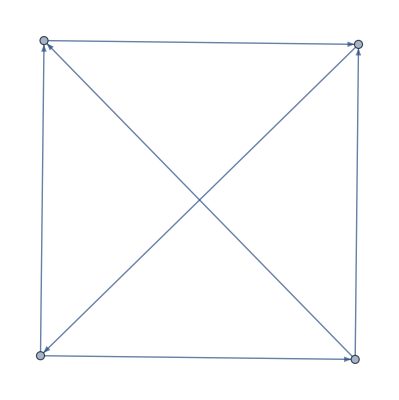
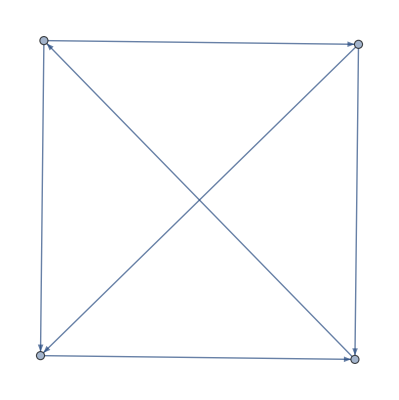
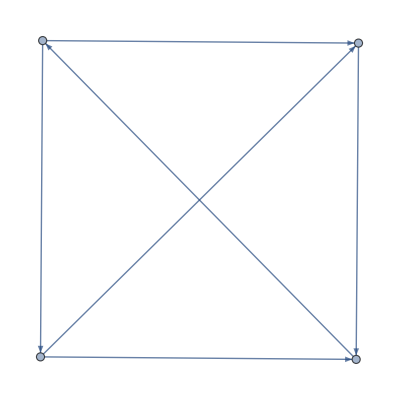
{-Graphics-,{2,5,6},3,1,1}
{-Graphics-,{3,4,6},3,1,1}
{-Graphics-,{1,4,6},3,1,1}
{-Graphics-,{6,3,6},3,1,1}
{-Graphics-,{2,5,6},3,1,1}
{-Graphics-,{1,4,6},3,1,1}
{-Graphics-,{6,3,6},3,1,1}
{-Graphics-,{3,4,6},3,1,1}

```mathematica
Map[{nthor[CompleteGraph[4],#],Join[{gtm[npsmat[nthor[CompleteGraph[4],#]]][[1]]},gtm[Transpose[AdjacencyMatrix[nthor[CompleteGraph[4],#]]]]],Length[FindCycle[nthor[CompleteGraph[4],#],∞,All]],VertexConnectivity[nthor[CompleteGraph[4],#]],EdgeConnectivity[nthor[CompleteGraph[4],#]]}&,{8,12,18,26,34,44,46,50}]//Column
```

```mathematica
npsmat[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})]]//MatrixForm
```

```mathematica
Table[Length[DeleteDuplicates[Flatten[FindPath[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})],i,j,∞,All]]]],{i,1,4},{j,1,4}]//MatrixForm
```

(0 | 2 | 3 | 4
4 | 0 | 4 | 3
3 | 4 | 0 | 2
2 | 3 | 4 | 0)

```mathematica
Table[Length[Flatten[FindPath[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})],i,j,∞,All]]],{i,1,4},{j,1,4}]//MatrixForm
```

(0 | 2 | 5 | 10
7 | 0 | 6 | 5
3 | 4 | 0 | 2
2 | 3 | 7 | 0)

```mathematica
Table[FindPath[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})],i,j,∞,All],{i,1,4},{j,1,4}]//MatrixForm
```

({} | {{1,2}} | {{1,3},{1,2,3}} | {{1,3,4},{1,2,4},{1,2,3,4}}
{{2,4,1},{2,3,4,1}} | {} | {{2,3},{2,4,1,3}} | {{2,4},{2,3,4}}
{{3,4,1}} | {{3,4,1,2}} | {} | {{3,4}}
{{4,1}} | {{4,1,2}} | {{4,1,3},{4,1,2,3}} | {})

```mathematica
Table[Select[FindPath[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})],i,j,∞,All],Length[#]>2&],{i,1,4},{j,1,4}]//MatrixForm
```

({} | {} | {{1,2,3}} | {{1,3,4},{1,2,4},{1,2,3,4}}
{{2,4,1},{2,3,4,1}} | {} | {{2,4,1,3}} | {{2,3,4}}
{{3,4,1}} | {{3,4,1,2}} | {} | {}
{} | {{4,1,2}} | {{4,1,3},{4,1,2,3}} | {})

```mathematica
Table[Length[Select[FindPath[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})],i,j,∞,All],Length[#]>2&]],{i,1,4},{j,1,4}]//MatrixForm
ArrayPlot[%]
```

(0 | 0 | 1 | 3
2 | 0 | 1 | 1
1 | 1 | 0 | 0
0 | 1 | 2 | 0)

-Graphics-

```mathematica
Table[PadLeft[Tally[Map[Length,FindPath[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 1}, {1, 0, 0, 0}})],i,j,∞,All]]],2],{i,1,4},{j,1,4}]//MatrixForm
```

((0
0) | (0
{2,1}) | ({2,1}
{3,1}) | ({3,2}
{4,1})
({3,1}
{4,1}) | (0
0) | ({2,1}
{4,1}) | ({2,1}
{3,1})
(0
{3,1}) | (0
{4,1}) | (0
0) | (0
{2,1})
(0
{2,1}) | (0
{3,1}) | ({3,1}
{4,1}) | (0
0))

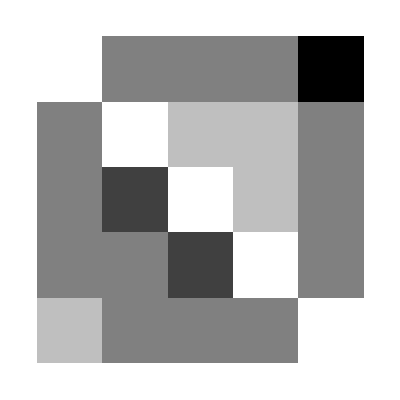
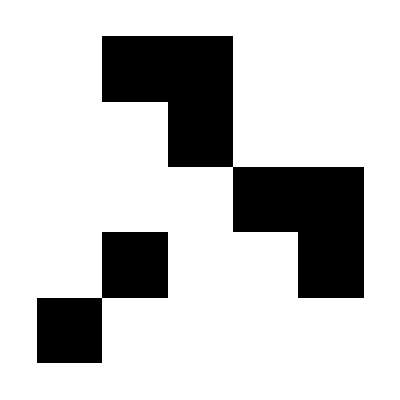
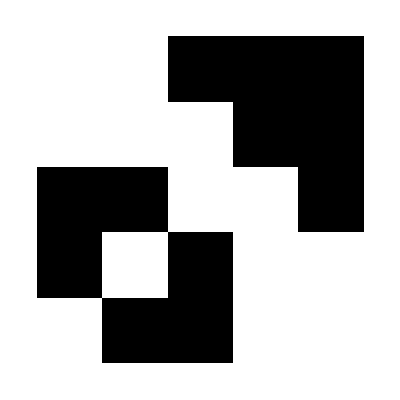
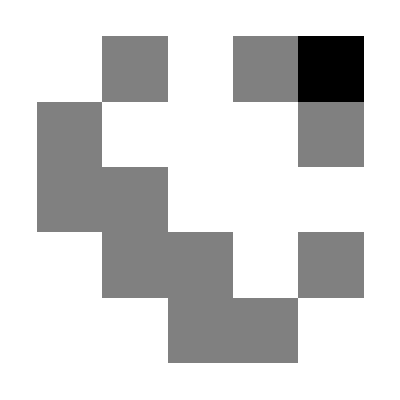
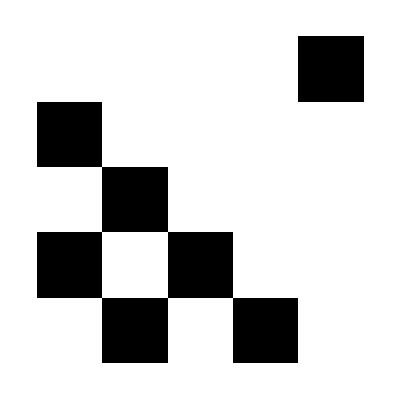

```mathematica
{ArrayPlot[Table[Length[Select[FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})],i,j,∞,All],Length[#]>0&]],{i,1,5},{j,1,5}]],
ArrayPlot[Table[Length[Select[FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})],i,j,∞,All],Length[#]==2&]],{i,1,5},{j,1,5}]],
ArrayPlot[Table[Length[Select[FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})],i,j,∞,All],Length[#]==3&]],{i,1,5},{j,1,5}]],
ArrayPlot[Table[Length[Select[FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})],i,j,∞,All],Length[#]==4&]],{i,1,5},{j,1,5}]],
ArrayPlot[Table[Length[Select[FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})],i,j,∞,All],Length[#]==5&]],{i,1,5},{j,1,5}]]}
```

```mathematica
Map[MatrixForm,Flatten[Table[{FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})],i,j,∞,All],FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})],j,i,∞,All]},{i,1,4},{j,i+1,5}],1]]//Column
```

({1,2} | {1,3,4,2}
{2,3,5,1} | {2,3,4,5,1})
({1,3} | {1,2,3}
{3,5,1} | {3,4,5,1})
({1,3,4} | {1,2,3,4}
{4,5,1} | {4,2,3,5,1})
({{1,3,5},{1,3,4,5},{1,2,3,5},{1,2,3,4,5}}
{{5,1}})
({{2,3}}
{{3,4,2},{3,5,1,2},{3,4,5,1,2}})
({{2,3,4}}
{{4,2},{4,5,1,2}})
({2,3,5} | {2,3,4,5}
{5,1,2} | {5,1,3,4,2})
({{3,4}}
{{4,2,3},{4,5,1,3},{4,5,1,2,3}})
({3,5} | {3,4,5}
{5,1,3} | {5,1,2,3})
({4,5} | {4,2,3,5}
{5,1,3,4} | {5,1,2,3,4})

Note that (2,3) is crucial to the balance between sides as it appears in paths to/from several values, but its cross (4,5) does not appear in a single to/from pair..

```mathematica
Quotient[3,2]
```

1

```mathematica
nthbit[x_,n_]:=Mod[Quotient[x,2^n],2]
```

```mathematica
nthbit[3,0]
```

1

```mathematica
Table[nthbit[Fibonacci[n],0],{n,1,100}]
Table[nthbit[Fibonacci[n],1],{n,1,100}]
Table[nthbit[Fibonacci[n],2],{n,1,100}]
Table[nthbit[Fibonacci[n],3],{n,1,100}]
Table[nthbit[Fibonacci[n],4],{n,1,100}]
```

{1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1,1,0,1}

{0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1,0,0,0,0,1,1}

{0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0,1,0,1,1,0,1,0,0,0,0,0,0}

{0,0,0,0,0,1,1,0,0,0,1,0,1,1,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,1,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,1,0,1,1,1,0,1,0,1,0,0,0,0,0,0,0,1,1,0,0,0,1,0,1,1,0,1,1,1,0,1,0,1,0,0,0,0,0,0}

{0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,1,1,1,0,0,0,1,0,1,1,0,1,1,0,1,0,0,0,0,1,1,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0,1,0,1,1,1,0,1,0,1,1,1,1,0,0,0,1,0,1,1,0,1,1,0,1,0,0,0,0,1,1,0,0,0,0,1,0,1,0,1,0,0,0,0,0,0}

```mathematica
tofrac[l_]:=FromDigits[l,2]/(2^(1+Length[l])-1)
tofrac[{1}]
```

1/3

```mathematica
dfrac[d_]:=Monitor[Block[{p=1,gs={}},While[gs=={},p++;gs=Select[Tally[Table[tofrac[Table[nthbit[Fibonacci[n],d],{n,1,m}]],{m,1,p}]],(Last[#]>1)&&(First[#]≠0)&]];gs][[1,1]],{p,m,n}]
```

```mathematica
dfrac[0]
```

3/7

```mathematica
dfrac[1]
```

2/21

```mathematica
dfrac[2]
```

2/91

```mathematica
dfrac[3]
```

202474/16777215

```mathematica
dfrac[4]
```

12352528810/4330384257087

```mathematica
dfrac[5]
```

30494933985423983216214/19347536633519984760328193

```mathematica
dfrac[6]
```

134810230311075930439717158555654706878239842646/374144441457457674818841471794196260589278699978753

```mathematica
dfrac[7]
```

26741734891899583507381967497816680143065139755168949551556298445360052238938799100154694825528662/139984046386113260483076552323936769829629381004690729274846099254769870219648685538816173958204751873

```mathematica
Map[{Numerator[#],Denominator[#]}&,{3/7,
2/21,
2/91,
202474/16777215,
12352528810/4330384257087,
30494933985423983216214/19347536633519984760328193,
134810230311075930439717158555654706878239842646/374144441457457674818841471794196260589278699978753}]
```

{{3,7},{2,21},{2,91},{202474,16777215},{12352528810,4330384257087},{30494933985423983216214,19347536633519984760328193},{134810230311075930439717158555654706878239842646,374144441457457674818841471794196260589278699978753}}

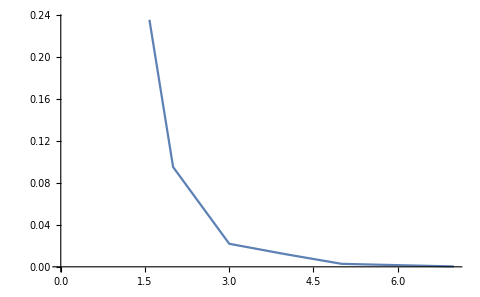

```mathematica
ListPlot[{3/7,
2/21,
2/91,
202474/16777215,
12352528810/4330384257087,
30494933985423983216214/19347536633519984760328193,
134810230311075930439717158555654706878239842646/374144441457457674818841471794196260589278699978753},Joined->True]
```

```mathematica
fib[l_]:=Append[l,l[[-1]]+l[[-2]]]
```

```mathematica
Nest[fib,{a+b,c+d},10]
```

{a+b,c+d,a+b+c+d,a+b+2 c+2 d,2 a+2 b+3 c+3 d,3 a+3 b+5 c+5 d,5 a+5 b+8 c+8 d,8 a+8 b+13 c+13 d,13 a+13 b+21 c+21 d,21 a+21 b+34 c+34 d,34 a+34 b+55 c+55 d,55 a+55 b+89 c+89 d}

```mathematica
f[2n]==f[2n-1]+f[2n-2]
f[2n-1]==f[2n-2]+f[2n-3]
f[2n]==f[2n-2]+f[2n-3]+f[2n-2]==2f[2n-2]+f[2n-3]
f[2n-2]==f[2n-3]+f[2n-4]
f[2n]==3f[2n-3]+2f[2n-4]
f[2n-3]==f[2n-4]+f[2n-5]
f[2n]==5f[2n-4]+3f[2n-5]
f[2n-4]==f[2n-5]+f[2n-6]
f[2n]==8f[2n-5]+5f[2n-6]
```

```mathematica
f[2n]==f[i+1]*f[2n-i]+f[i]*f[2n-(i+1)]
i==n->f[2n]==f[n+1]*f[n]+f[n]*f[n-1]
i==n-1->f[2n]==f[n]*f[n-1]+f[n-1]*f[n-2]

f[2n]==f[n-1](f[n-1]+2f[n-2])
f[2n+2]==f[n](f[n]+2f[n-1])

f[x]==f[i+1]*f[x-i]+f[i]*f[x-(i+1)]
f[x-1]==f[i+1]*f[x-i-1]+f[i]*f[x-i-2]
f[x-2]==f[i+1]*f[x-i-2]+f[i]*f[x-i-3]
```

```mathematica
f[n^2]==f[i+1]*f[n^2-i]+f[i]*f[n^2-(i+1)]

f[n^2]==f[n^2-n+1]*f[n]+f[n^2-n]*f[n+1]

i==n^2-n->f[n^2]==f[n^2-n+1]*f[n]+f[n^2-n]*f[n-1]

f[n^2-1n]==f[n+1]*f[n^2-2n]+f[n]*f[n^2-2n-1]
f[n^2-2n]==f[n+1]*f[n^2-3n]+f[n]*f[n^2-3n-1]
f[n^2-3n]==f[n+1]*f[n^2-4n]+f[n]*f[n^2-4n-1]
f[2n]==f[n+1]*f[n]+f[n]*f[n-1]
```

```mathematica
Expand[n^2-(n-2)n]
```

2 n

```mathematica
n-1==x
```

```mathematica
Table[{n,Fibonacci[n]},{n,1,10}]
```

{{1,1},{2,1},{3,2},{4,3},{5,5},{6,8},{7,13},{8,21},{9,34},{10,55}}

```mathematica
{1,2,3}[[-1]]
```

3

```mathematica
4^x==6^x-3
6^x-4^x==3
f[x]:=6^x-4^x,3
```

```mathematica
g[z]==a+∑_(n=1)^∞ Limit[(z-f[a])^n/(n!)D[((w-a)/(f[w]-f[a]))^n,w,n-1],w->a]
```

```mathematica
FullSimplify[(w-0)/(6^w-4^w-6^0+4^0)]
```

w/(-4^w+6^w)

```mathematica
N[∑_(n=1)^∞ Limit[FullSimplify[(3)^n/(n!)D[w/(-4^w+6^w),{w,n-1}]],w->0]]
```

D::dvar: Multiple derivative specifier {w, 15.} does not have the form {variable, n}, where n is a non-negative machine integer.

General::ivar: 1/w is not a valid variable.

$Aborted

```mathematica
Table[Limit[FullSimplify[(3)^n/(n!)D[w/(-4^w+6^w),{w,n-1}]],w->0],{n,1,3}]//Column
```

3/Log[3/2]
-(9 (Log[2]^2-Log[3]^2-Log[4]^2+Log[6] Log[9]))/(4 Log[3/2]^2)
(3 (Log[4]^4+3 Log[4]^2 Log[6]^2-12 Log[4] Log[6]^3+Log[6] (3 Log[6]^3+3 Log[6] Log[9]^2-2 Log[9]^3+Log[6]^2 Log[576])))/(4 Log[3/2]^3)

```mathematica
N[3/Log[3/2]-(9 (Log[2]^2-Log[3]^2-Log[4]^2+Log[6] Log[9]))/(4 Log[3/2]^2)+(3 (Log[4]^4+3 Log[4]^2 Log[6]^2-12 Log[4] Log[6]^3+Log[6] (3 Log[6]^3+3 Log[6] Log[9]^2-2 Log[9]^3+Log[6]^2 Log[576])))/(4 Log[3/2]^3)]
```

17.6347

```mathematica
Expand[D[w/(3^w-2^w),{w,2}]]
```

(2^(1+w) Log[2])/((-2^w+3^w)^2)+(2^(1+2 w) w Log[2]^2)/((-2^w+3^w)^3)+(2^w w Log[2]^2)/((-2^w+3^w)^2)-(2 3^w Log[3])/((-2^w+3^w)^2)-(2^(2+w) 3^w w Log[2] Log[3])/((-2^w+3^w)^3)+(2 3^(2 w) w Log[3]^2)/((-2^w+3^w)^3)-(3^w w Log[3]^2)/((-2^w+3^w)^2)

```mathematica
Table[Expand[D[w/(3^w-2^w),{w,i}]],{i,1,4}]//Column
```

1/(-2^w+3^w)+(2^w w Log[2])/((-2^w+3^w)^2)-(3^w w Log[3])/((-2^w+3^w)^2)
(2^(1+w) Log[2])/((-2^w+3^w)^2)+(2^(1+2 w) w Log[2]^2)/((-2^w+3^w)^3)+(2^w w Log[2]^2)/((-2^w+3^w)^2)-(2 3^w Log[3])/((-2^w+3^w)^2)-(2^(2+w) 3^w w Log[2] Log[3])/((-2^w+3^w)^3)+(2 3^(2 w) w Log[3]^2)/((-2^w+3^w)^3)-(3^w w Log[3]^2)/((-2^w+3^w)^2)
(3 2^(1+2 w) Log[2]^2)/((-2^w+3^w)^3)+(3 2^w Log[2]^2)/((-2^w+3^w)^2)+(3 2^(1+3 w) w Log[2]^3)/((-2^w+3^w)^4)+(3 2^(1+2 w) w Log[2]^3)/((-2^w+3^w)^3)+(2^w w Log[2]^3)/((-2^w+3^w)^2)-(2^(2+w) 3^(1+w) Log[2] Log[3])/((-2^w+3^w)^3)-(2^(1+2 w) 3^(2+w) w Log[2]^2 Log[3])/((-2^w+3^w)^4)-(6^(1+w) w Log[2]^2 Log[3])/((-2^w+3^w)^3)+(2 3^(1+2 w) Log[3]^2)/((-2^w+3^w)^3)-(3^(1+w) Log[3]^2)/((-2^w+3^w)^2)+(2^(1+w) 3^(2+2 w) w Log[2] Log[3]^2)/((-2^w+3^w)^4)-(6^(1+w) w Log[2] Log[3]^2)/((-2^w+3^w)^3)-(2 3^(1+3 w) w Log[3]^3)/((-2^w+3^w)^4)+(2 3^(1+2 w) w Log[3]^3)/((-2^w+3^w)^3)-(3^w w Log[3]^3)/((-2^w+3^w)^2)
(3 2^(3+3 w) Log[2]^3)/((-2^w+3^w)^4)+(3 2^(3+2 w) Log[2]^3)/((-2^w+3^w)^3)+(2^(2+w) Log[2]^3)/((-2^w+3^w)^2)+(3 2^(3+4 w) w Log[2]^4)/((-2^w+3^w)^5)+(9 2^(2+3 w) w Log[2]^4)/((-2^w+3^w)^4)+(3 2^(1+2 w) w Log[2]^4)/((-2^w+3^w)^3)+(2^(3+2 w) w Log[2]^4)/((-2^w+3^w)^3)+(2^w w Log[2]^4)/((-2^w+3^w)^2)-(2^(3+2 w) 3^(2+w) Log[2]^2 Log[3])/((-2^w+3^w)^4)-(2^(3+w) 3^(1+w) Log[2]^2 Log[3])/((-2^w+3^w)^3)-(2^(5+3 w) 3^(1+w) w Log[2]^3 Log[3])/((-2^w+3^w)^5)-(2^(3+2 w) 3^(2+w) w Log[2]^3 Log[3])/((-2^w+3^w)^4)-(2^(3+w) 3^w w Log[2]^3 Log[3])/((-2^w+3^w)^3)+(2^(3+w) 3^(2+2 w) Log[2] Log[3]^2)/((-2^w+3^w)^4)-(2^(3+w) 3^(1+w) Log[2] Log[3]^2)/((-2^w+3^w)^3)+(2^(4+2 w) 3^(2+2 w) w Log[2]^2 Log[3]^2)/((-2^w+3^w)^5)-(2^(2+2 w) 3^(2+w) w Log[2]^2 Log[3]^2)/((-2^w+3^w)^4)+(2^(2+w) 3^(2+2 w) w Log[2]^2 Log[3]^2)/((-2^w+3^w)^4)-(2^(2+w) 3^(1+w) w Log[2]^2 Log[3]^2)/((-2^w+3^w)^3)-(8 3^(1+3 w) Log[3]^3)/((-2^w+3^w)^4)+(8 3^(1+2 w) Log[3]^3)/((-2^w+3^w)^3)-(4 3^w Log[3]^3)/((-2^w+3^w)^2)-(2^(5+w) 3^(1+3 w) w Log[2] Log[3]^3)/((-2^w+3^w)^5)+(2^(3+w) 3^(2+2 w) w Log[2] Log[3]^3)/((-2^w+3^w)^4)-(2^(3+w) 3^w w Log[2] Log[3]^3)/((-2^w+3^w)^3)+(8 3^(1+4 w) w Log[3]^4)/((-2^w+3^w)^5)-(4 3^(2+3 w) w Log[3]^4)/((-2^w+3^w)^4)+(8 3^(2 w) w Log[3]^4)/((-2^w+3^w)^3)+(2 3^(1+2 w) w Log[3]^4)/((-2^w+3^w)^3)-(3^w w Log[3]^4)/((-2^w+3^w)^2)

```mathematica
Table[i!/{1,1,2,3,4,6,6,12,15,20,30,30,60,60,84,105,140,210,210,420,420,420,420,840,840,1260,1260,1540,2310,2520,4620,4620,5460,5460,9240,9240,13860,13860,16380,16380,27720,30030,32760,60060,60060,60060,60060,120120}[[i]],{i,1,48}]
```

{1,2,3,8,30,120,840,3360,24192,181440,1330560,15966720,103783680,1452971520,15567552000,199264665600,2540624486400,30487493836800,579262382899200,5792623828992000,121645100408832000,2676192208994304000,61552420806868992000,738629049682427904000,18465726242060697600000,320072588195718758400000,8641959881284406476800000,197979444553060948377600000,3827602594692511668633600000,105259071354044070887424000000,1779835206532017925914624000000,56954726609024573629267968000000,1590351212236609248263405568000000,54071941216044714440955789312000000,1118306056968197503210676551680000000,40259018050855110115584355860480000000,993055778587759382851080777891840000000,37736119586334856548341069559889920000000,1245291946349050266095255295476367360000000,49811677853962010643810211819054694400000000,1206801104370988712415947404525279641600000000,46786750507921408542895191683133918412800000000,1844177749187235520065785472176861950771200000000,44260265980493652481578851332244686818508800000000,1991711969122214361671048309951010906832896000000000,91618750579621860636868222257746501714313216000000000,4306081277242227449932806446114085580572721152000000000,103345950653813458798387354706738053933745307648000000000}

```mathematica
npsmat[]//MatrixForm
```

```mathematica
EdgeList[AdjacencyGraph[({{0, 1, 1, 0}, {0, 0, 1, 1}, {0, 0, 0, 0}, {1, 0, 0, 0}})]]
```

{1->2,1->3,2->3,2->4,3->4,4->1}

```mathematica
DeleteDuplicates[Map[MatrixForm,Table[npsmat[Graph[Map[ps[[i]][[#[[1]]]]->ps[[i]][[#[[2]]]]&,{1->2,2->3,3->4,4->1,4->2,4->3}]]],{i,1,24}]]]
```

{(0 | 1 | 1 | 1
1 | 0 | 1 | 1
1 | 2 | 0 | 1
1 | 2 | 3 | 0)}

```mathematica
ps[[3]]
```

{1,3,2,4}

```mathematica
ps=Permutations[{1,2,3,4}];
%//Length
```

24

```mathematica
Map[MatrixForm,Flatten[Table[{FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})],i,j,∞,All],FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})],j,i,∞,All]},{i,1,4},{j,i+1,5}],1]]//Column
```

({{1,2},{1,3,4,2}}
{{2,3,5,1}})
({{1,3},{1,2,3}}
{{3,5,1}})
({{1,3,4},{1,2,3,4}}
{{4,2,3,5,1}})
({{1,3,5},{1,2,3,5}}
{{5,1}})
({{2,3}}
{{3,4,2},{3,5,1,2}})
({2,3,4}
{4,2})
({{2,3,5}}
{{5,1,2},{5,1,3,4,2}})
({3,4}
{4,2,3})
({{3,5}}
{{5,1,3},{5,1,2,3}})
({{4,2,3,5}}
{{5,1,3,4},{5,1,2,3,4}})

```mathematica
SortBy[Tally[Flatten[Map[pairs,Flatten[Table[{FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})],i,j,∞,All],FindPath[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})],j,i,∞,All]},{i,1,4},{j,i+1,5}],3]],1]],Last]
```

{{{1,3},7},{{4,2},7},{{1,2},8},{{3,4},9},{{3,5},9},{{5,1},11},{{2,3},12}}

```mathematica
{({{0, 8, 7, 0, 0}, {0, 0, 12, 0, 0}, {0, 0, 0, 9, 9}, {0, 7, 0, 0, 0}, {11, 0, 0, 0, 0}})//MatrixForm,npsmat[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})]]//MatrixForm}
```

{(0 | 8 | 7 | 0 | 0
0 | 0 | 12 | 0 | 0
0 | 0 | 0 | 9 | 9
0 | 7 | 0 | 0 | 0
11 | 0 | 0 | 0 | 0),(0 | 2 | 2 | 2 | 2
1 | 0 | 1 | 1 | 1
1 | 2 | 0 | 1 | 1
1 | 1 | 1 | 0 | 1
1 | 2 | 2 | 2 | 0)}

```mathematica
Eigenvalues[({{0, 2, 2, 2, 2}, {1, 0, 1, 1, 1}, {1, 2, 0, 1, 1}, {1, 1, 1, 0, 1}, {1, 2, 2, 2, 0}})]//N
```

{5.38049,-1.51503+0.426592 ⅈ,-1.51503-0.426592 ⅈ,-1.35044,-1.}

```mathematica
Eigenvalues[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})]//N
```

{1.39534,-0.460355+1.13932 ⅈ,-0.460355-1.13932 ⅈ,-0.474627,0.}

```mathematica
({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}}).({{0, 2, 2, 2, 2}, {1, 0, 1, 1, 1}, {1, 2, 0, 1, 1}, {1, 1, 1, 0, 1}, {1, 2, 2, 2, 0}}).Transpose[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})]//MatrixForm
```

(3 | 1 | 4 | 2 | 2
2 | 0 | 2 | 2 | 1
6 | 3 | 3 | 3 | 2
1 | 1 | 2 | 0 | 1
4 | 2 | 4 | 2 | 0)

```mathematica
pairs[l_]:=Table[{l[[i]],l[[i+1]]},{i,1,Length[l]-1}]
```

```mathematica
graphs->orientations->path list matrices -> properties
{x-sym,( extended x-sym), relative counts, key edges, v-conn, e-conn, diameter, girth,{SuperPlus[d]-SuperMinus[d]}}⊂properties
```

```mathematica
VertexInDegree[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})]]
```

{1,2,2,1,1}

```mathematica
VertexOutDegree[AdjacencyGraph[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 1, 1}, {0, 1, 0, 0, 0}, {1, 0, 0, 0, 0}})]]
```

{2,1,2,1,1}

```mathematica
{1,2,2,1,1}-{2,1,2,1,1}
```

{-1,1,0,0,0}

```mathematica
VertexInDegree[AdjacencyGraph[#]]-VertexOutDegree[AdjacencyGraph[#]]&[({{0, 1, 1, 0, 0}, {0, 0, 1, 0, 0}, {0, 0, 0, 0, 1}, {0, 1, 0, 0, 1}, {1, 0, 0, 0, 0}})]
Total[%]
```

{-1,1,1,-2,1}

0

```mathematica
∑SuperPlus[Subscript[d, i]]==∑SuperMinus[Subscript[d, i]]
```

```mathematica
"In-out radius r branching from vertex."
```

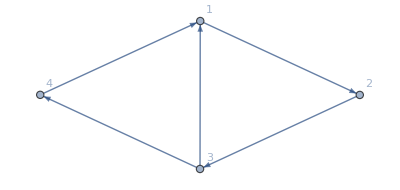

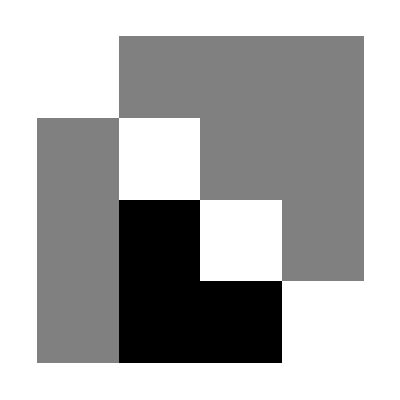
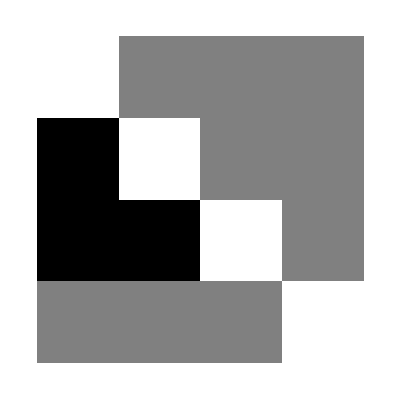
{(0 | 1 | 0 | 0
0 | 0 | 1 | 0
1 | 0 | 0 | 1
1 | 0 | 0 | 0),(0 | 1 | 1 | 1
2 | 0 | 1 | 1
2 | 2 | 0 | 1
1 | 1 | 1 | 0),-Graphics-,-Graphics-,-Graphics-}

(4 | 2
3 | 1)

```mathematica
Graph[{1->2,2->3,3->1,3->4,4->1},VertexLabels->"Name"]
{AdjacencyMatrix[Graph[{1->2,2->3,3->1,3->4,4->1}]]//MatrixForm,
npsmat[Graph[{1->2,2->3,3->1,3->4,4->1}]]//MatrixForm,
AdjacencyMatrix[Graph[{1->2,2->3,3->1,3->4,4->1}]]//ArrayPlot,
Map[Reverse,Transpose[Map[Reverse,npsmat[Graph[{1->2,2->3,3->1,3->4,4->1}]]]]]//ArrayPlot,
npsmat[Graph[{1->2,2->3,3->1,3->4,4->1}]]//ArrayPlot}
```

```mathematica
N[√(10/4)]
```

1.58114

```mathematica
AdjacencyMatrix[CompleteGraph[4]]//MatrixForm
```

```mathematica
{MatrixForm[npsmat[AdjacencyGraph[({{0, 1, 1, 1}, {1, 0, 1, 1}, {1, 1, 0, 1}, {1, 1, 1, 0}})]]],MatrixForm[npsmat[AdjacencyGraph[({{0, 1, 1, 1}, {0, 0, 1, 1}, {0, 0, 0, 1}, {0, 0, 0, 0}})]]]}
```

{(0 | 5 | 5 | 5
5 | 0 | 5 | 5
5 | 5 | 0 | 5
5 | 5 | 5 | 0),(0 | 5 | 5 | 5
5 | 0 | 5 | 5
5 | 5 | 0 | 5
5 | 5 | 5 | 0)}

```mathematica
npsmat[AdjacencyGraph[({{0, 1, 1, 1}, {1, 0, 0, 1}, {1, 1, 0, 1}, {0, 1, 1, 0}})]]//MatrixForm
```

(0 | 5 | 3 | 4
2 | 0 | 3 | 3
3 | 4 | 0 | 5
3 | 3 | 2 | 0)

```mathematica
Table[Total[Sort[Flatten[Map[edgeNums[#,4]&,FindPath[CompleteGraph[4],i,j,∞,All]]]]],{i,1,4},{j,1,4}]//MatrixForm
```

(0 | -7 | 6 | 31
7 | 0 | 4 | 29
-6 | -4 | 0 | 10
-31 | -29 | -10 | 0)

```mathematica
edgeNum[i_,j_,n_]:=If[i<j,j-1/2 i (1+i-2 n)-n,-(i-1/2 j(1+j-2 n)-n)]
```

```mathematica
edgeNums[l_,n_]:=Table[edgeNum[l[[i]],l[[i+1]],n],{i,1,Length[l]-1}]
```

```mathematica
Table[FullSimplify[InterpolatingPolynomial[Table[{Map[{#[[1]],#[[2]]}&,EdgeList[CompleteGraph[n]]][[i]],i},{i,1,1/2(n)(n-1)}],{i,j}]],{n,3,10}]//Column
```

-2+i+j
-4-1/2 (-7+i) i+j
-5-1/2 (-9+i) i+j
-6-1/2 (-11+i) i+j
-7-1/2 (-13+i) i+j
-8-1/2 (-15+i) i+j
-9-1/2 (-17+i) i+j
-10-1/2 (-19+i) i+j

```mathematica
FullSimplify[-n-1/2(i-(2n-1))i+j]
```

j-1/2 i (1+i-2 n)-n

```mathematica
FullSimplify[3+(3+1/2 (-2+n)) (-1+n)]
```

1/2 (1+n) (2+n)